```mathematica
(* Mathematica code for renormalization of piecewise linear circle homeomorphisms. *)
(* See J. Belk, J. Hyde, and J. Moore, A piecewise linear homeomorphism of the circle which is periodic under renormalization. *)
```

```mathematica
(* Initial setup code for renormalization *)
MaxCircleStarIterations=500; (* Change to increase the maximum number of stars computed. *)
functionlist=Hold[{PLCircleMap,x1,y1,x2,y2,slope,InversePiece,ApplyLinearMap,IsCollinear,CombinePieces,Pieces,DomainBreakpoints,AllBreakpoints,IdentityCircleMap,FixPiece,Simplify,Inverse,NonCommutativeMultiply,Power,Equal,Unequal,ShowGraph,CircleRotation,Restriction,MinRotations,RotationNumberEqualPair,GetAlgebraic,RotationNumber,IntervalExchange,IntervalExchangeRotate}];
Unprotect@@functionlist;
x1[piece_]:=First@First@piece
y1[piece_]:=Last@First@piece
x2[piece_]:=First@Last@piece
y2[piece_]:=Last@Last@piece
slope[piece_]:=(y2[piece]-y1[piece])/(x2[piece]-x1[piece])
InversePiece[piece_]:=Reverse/@piece
ApplyLinearMap[piece_,x_]:=y1[piece]+slope[piece](x-x1[piece])
IsCollinear[piece1_,piece2_]:=(Last[piece1]==First[piece2])&&(slope[piece1]==slope[piece2])
CombinePieces[piece1_,piece2_]:={First@piece1,Last@piece2}
Pieces[f_PLCircleMap]:=List@@f
DomainBreakpoints[f_PLCircleMap]:=Append[x1/@Pieces[f],1]
AllBreakpoints[f_PLCircleMap]:=Union@@(Pieces@f)
IdentityCircleMap=PLCircleMap[{{0,0},{1,1}}];
FixPiece[L_]:={
{If[x1@L==1,0,x1@L],If[y1@L==1,0,y1@L]},
{If[x2@L==0,1,x2@L],If[y2@L==0,1,y2@L]}
}
Simplify[f_PLCircleMap]:=Module[{curpiece=First@f},
PLCircleMap@@Last@Last@Reap@(
Do[
If[
IsCollinear[curpiece,newpiece],
curpiece=CombinePieces[curpiece,newpiece],
Sow[curpiece];curpiece=newpiece
],
{newpiece,List@@(Rest@f)}
];
Sow[curpiece])
]
f_PLCircleMap[x_?NumericQ]:=ApplyLinearMap[SelectFirst[f,x<=x2[#]&],x]
Inverse[f_PLCircleMap]:=
With[{k=SelectFirst[Range@Length@f,y1[f[[#]]]==0&]},
PLCircleMap@@(InversePiece/@Join[f[[k;;]],f[[;;k-1]]])
]
NonCommutativeMultiply[f_PLCircleMap,g_PLCircleMap]:=
With[{
breakpoints=Sort[
Union[
FullSimplify[DomainBreakpoints@g],
FullSimplify[Inverse[g]/@DomainBreakpoints[f]]
],
Less]
},
Simplify@(PLCircleMap@@Table[
FixPiece[{
{breakpoints[[k]],FullSimplify@f@g@breakpoints[[k]]},
{breakpoints[[k+1]],FullSimplify@f@g@breakpoints[[k+1]]}
}],
{k,1,Length@breakpoints-1}])
]
Power[f_PLCircleMap,n_Integer]:=Which[
n<0,Inverse[f]^(-n),
n==0,IdentityCircleMap,
n==1,f,
True,NonCommutativeMultiply@@ConstantArray[f,n]
]
Power[f_PLCircleMap,g_PLCircleMap]:=Inverse[g]**f**g
Equal[f1_PLCircleMap,f2_PLCircleMap]:=(Pieces@f1==Pieces@f2)
Unequal[f1_PLCircleMap,f2_PLCircleMap]:=!(f1==f2)
ShowGraph[f_PLCircleMap]:=
Graphics[{
AbsolutePointSize[Min[5,100./Length[f]]],
Table[
Tooltip[Line[piece],"slope "<>ToString[slope[piece],InputForm]],
{piece,Pieces@f}
],
Table[
Tooltip[Point[p],"("<>ToString[p⟦1⟧,InputForm]<>", "<>ToString[p⟦2⟧,InputForm]<>")"],{p,AllBreakpoints@f}
]
},Frame->True,FrameStyle->Directive[{Thick,Black}],PlotRange->{{0,1},{0,1}},
GridLines->{Range[1,7]/8,Range[1,7]/8},
FrameTicks->{
{0,{1/4,"1/4"},{1/2,"1/2"},{3/4,"3/4"},1},
{0,{1/4,"1/4"},{1/2,"1/2"},{3/4,"3/4"},1},
{},
{}
},
FrameTicksStyle->12]
CircleRotation[theta_]:=If[Mod[theta,1]==0,
IdentityCircleMap,
PLCircleMap[{{0,Mod[theta,1]},{1-Mod[theta,1],1}},{{1-Mod[theta,1],0},{1,Mod[theta,1]}}]
]
Restriction[f_PLCircleMap,{a_,b_}]:=
Join@@Table[
Which[
a<=x1[p]&&x2[p]<=b,{p},
x2[p]<=a||b<=x1[p],{},
x1[p]<=a&&x2[p]>=b,{FixPiece@{{a,ApplyLinearMap[p,a]},{b,ApplyLinearMap[p,b]}}},
x1[p]<a&&a<x2[p]<b,{FixPiece@{{a,ApplyLinearMap[p,a]},Last@p}},
a<x1[p]<b&&x2[p]>b,{FixPiece@{First@p,{b,ApplyLinearMap[p,b]}}}
],
{p,Pieces@f}]
NumFixedPoints[f_PLCircleMap]:=NumFixedPoints[f]=Sum[
Which[x1[p]==y1[p]&&x2[p]==y2[p],Infinity,
x1[p]==y1[p],1,
(x1[p]-y1[p])(x2[p]-y2[p])<0,1,
True,0],
{p,Pieces@f}]
(* MinRotations computes the number mf in the paper. *)
MinRotations[f_PLCircleMap]:=If[NumFixedPoints[f]>0,Infinity,
With[{F=Inverse[f],r=f[0]},First@NestWhile[{#[[1]]+1,F[#[[2]]]}&,{1,F[0]},#[[2]]!=1&&#[[2]]>=r&]]
]
CircleStar[f_PLCircleMap]:=CircleStar[f]=If[NumFixedPoints[f]>0,IdentityCircleMap,
With[{r=f[0],mf=MinRotations@f,F=Inverse[f]},
FullSimplify@Simplify[PLCircleMap@@(Join[
Restriction[F^mf,{0,(f^mf)[r]}],
Restriction[F^(mf+1),{(f^mf)[r],r}]
]/r)]]]
RotationNumberEqualPair[f_PLCircleMap]:=
With[{results=NestWhileList[{CircleStar[#[[1]]],#[[2]]+1}&,{f,0},Length@Union[First/@{##},SameTest->Equal]==Length[First/@{##}]&,All,MaxCircleStarIterations]},
With[{lastone=First@Last@results},
{Last@SelectFirst[results,First[#]==lastone&],Last@Last@results}
]]
GetAlgebraic[{first_,second_},minrotationdata_]:=
Which[first>0,
1/(First@minrotationdata+GetAlgebraic[{first-1,second-1},Rest@minrotationdata]),
First@minrotationdata==Infinity,
0,
True,
Module[{x},SelectFirst[SolveValues[Fold[Simplify[1/#1-#2]&,x,minrotationdata]==x,x],0<=#<=1&]]
]
RotationNumber[f_PLCircleMap]:=
With[{pair=RotationNumberEqualPair@f},
Module[{minrotationdata=MinRotations/@NestList[CircleStar,f,pair[[2]]-1]},
If[pair[[1]]>=2&&Nest[CircleStar,f,pair[[1]]]==IdentityCircleMap&&NumFixedPoints@Nest[CircleStar,f,pair[[1]]-1]>0,
With[{g=Nest[CircleStar,f,pair[[1]]-2]},
If[NumFixedPoints[g^(MinRotations[g])]==0,minrotationdata[[pair[[1]]-2+1]]=MinRotations[g]+1]
]
];
Simplify@GetAlgebraic[pair,minrotationdata]
]]
IntervalExchange[q_]:=PLCircleMap[{{0,1/(q+1)},{1/(q+1),1}},{{1/(q+1),0},{1,1/(q+1)}}]
IntervalExchangeRotate[q_,r_]:=CircleRotation[r]**IntervalExchange[q]
Protect@@functionlist;
```

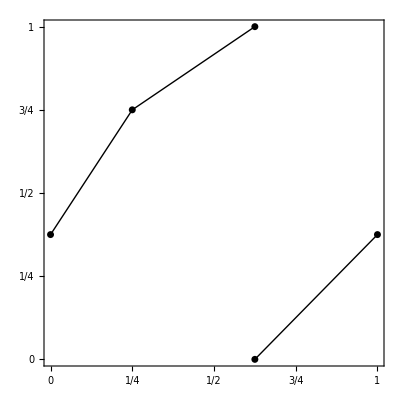

PLCircleMap[{{0,4/9},{1/3,2/3}},{{1/3,2/3},{5/9,1}},{{5/9,0},{1,4/9}}]

True

{0,2}

-1+√2

True

1/(√2)

```mathematica
(* Example from Theorem 4 in the paper. *)
f=PLCircleMap[{{0,3/8},{1/4,3/4}},{{1/4,3/4},{5/8,1}},{{5/8,0},{1,3/8}}];
ShowGraph[f]
CircleStar@f
CircleStar@CircleStar@f==f
RotationNumberEqualPair[f]
RotationNumber[f]
CircleStar@IntervalExchangeRotate[2/3,1/5]==f
RotationNumber@IntervalExchangeRotate[2/3,1/5]
```

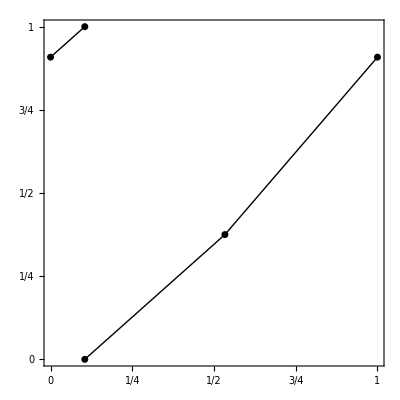

{148,149}

668882489207594075334619723191244632191899781818066714800164040622/761960058189671511292372730373166431351657862332319255996727602151

```mathematica
ShowGraph@IntervalExchangeRotate[7/8,3/8]
RotationNumberEqualPair@IntervalExchangeRotate[7/8,3/8]
RotationNumber@IntervalExchangeRotate[7/8,3/8]
```

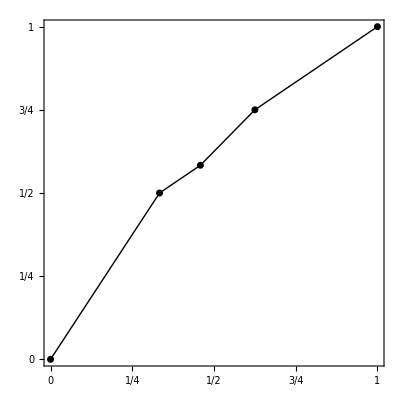
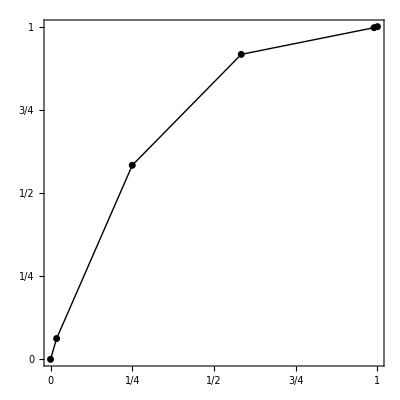

True

```mathematica
(* F obstruction *)
g=PLCircleMap[
{{0,0},{1/3,1/2}},
{{1/3,1/2},{11/24,7/12}},
{{11/24,7/12},{5/8,3/4}},
{{5/8,3/4},{1,1}}];
h=PLCircleMap[
{{0,0},{1/54,1/16}},
{{1/54,1/16},{1/4,7/12}},
{{1/4,7/12},{7/12,11/12}},
{{7/12,11/12},{95/96,323/324}},
{{95/96,323/324},{1,1}}
];
{ShowGraph[g],ShowGraph[h]}
CircleStar@IntervalExchangeRotate[2/3,1/5]==
PLCircleMap@@Join[
3*Restriction[g,{1/4,(g^(-1))[7/12]}]-3/4,
3*Restriction[Inverse[h]**g,{(g^(-1))[7/12],7/12}]-3/4
]
```